#### Importing data from Julia

```mathematica
SetDirectory[NotebookDirectory[]];
datawignermix=Import["Wopentest.dat"];
sp=Import["survivalprobability.dat"];
```

```mathematica
wigner2=ListDensityPlot[datawignermix,PlotRange->{{-5,5},{-5,5},All},Frame->True,FrameLabel->{"x","p"},LabelStyle->Directive[Bold,Medium],ColorFunction->"TemperatureMap",PlotLegends->Automatic]
```

-Graphics-

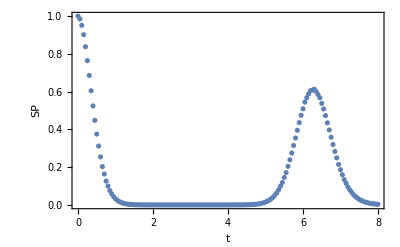

```mathematica
ListPlot[sp,Frame->True,FrameLabel->{"t","SP"},LabelStyle->Directive[Bold, Medium]]
```